## Math 2325 Project 4 (Chapter 11) - Sequences and Series

Helmut Knaust, Department of Mathematical Sciences, UTEP, El Paso TX 79968
hknaust@utep.edu
11/18/2003. Last edits 11/19/2023

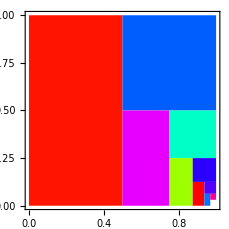
## 

## The Programs

### Filling a Unit Square

The command produces Figure 11.1 on p. 184 (p.177). The page numbers in blue are for the PDF-version of the textbook.

You can change the value of n to see more or less rectangles.

```mathematica
n=4;
obj[k_]:={{Hue[RandomReal[]],Rectangle[{1-2^(-k),0},{1-2^(-k-1),2^(-k)}]},{Hue[RandomReal[]],Rectangle[{1-2^(-k-1),2^(-k-1)},{1,2^(-k)}]}}
Show[Graphics[Table[obj[k],{k,0,n}]],AspectRatio->1,PlotRange->{{0,1},{0,1}},Frame->True]
Clear[n];
```

### Sequences and Series

The command below produces output similar to Figure 11.4 on p. 188 in the textbook (p. 181).

The first input is the sequence a_k you are summing. You must use the variable name k.
The sums are computed starting at the second input and ending at the third input.

```mathematica
CalcWin1[expr__,start_,end_]:=Module[{st=start,gr1,gr2,final=end,n,s,fct=expr},s[st-1]=0;s[n_]:=s[n]=N[s[n-1]+fct/.{k->n}];gr1=Graphics[Table[{Blue,Line[{{s[n],0},{s[n],1}}]},{n,st,final}],Axes->{Automatic,None},PlotRange->All,PlotLabel->Text["s_n"], BaseStyle->{FontSize->14},AspectRatio->.3,ImageSize->500];gr2=Graphics[Table[{Red,Line[{{fct/.{k->n},0},{fct/.{k->n},1}}]},{n,st,final}],Axes->{Automatic,None},PlotRange->All,PlotLabel->Text["a_n"],BaseStyle->{FontSize->14},AspectRatio->.3];GraphicsGrid[{{gr1},{gr2}}]]
```

```mathematica
CalcWin1[1/k,1,15]
```

A different visualization of the same data:

```mathematica
CalcWin2[expr__,start_,end_]:=Module[{st=start,gr1,gr2,final=end,n,s,fct=expr},s[st-1]=0;s[n_]:=s[n]=N[s[n-1]+fct/.{k->n}];gr1=Print@Graphics[Table[{Blue,AbsolutePointSize[5],Point[{n,s[n]}]},{n,st,final}],Axes->{Automatic},AxesOrigin->{0,0},PlotRange->All,PlotLabel->Text["s_n"], BaseStyle->{FontSize->14},AspectRatio->.3,ImageSize->600];gr2=Print@Graphics[Table[{Red,AbsolutePointSize[5],Point[{n,fct/.{k->n}}]},{n,st,final}],Axes->{Automatic},AxesOrigin->{0,0},PlotRange->All,PlotLabel->Text["a_n"],BaseStyle->{FontSize->14},AspectRatio->.3,ImageSize->600]]
```

```mathematica
CalcWin2[1/k,1,20]
```

If you want to change the code above (and below) to work for the sequence a_k=12(-1)^(k+1)/(2k-1) for example, type “12 (-1)^(k+1)/(2k-1)” instead of “1/k”.

### Partial Sums and J(n)

Next we compute (numerical) partial sums of the harmonic series and  J(n) - see p.185 (p. 179) in the textbook for the definition.

```mathematica
NSum[1/k,{k,1,10}]
```

```mathematica
NSum[1/k,{k,1,11}]
```

```mathematica
J[n_]:=Ceiling[NSum[1/k,{k,1,n}]]
```

```mathematica
J[11]
```

### Stopwatch

The command below runs for 60 seconds of CPU time.

Every 6 seconds it tells you how many terms of the partial sum of the harmonic series have been computed so far, and what the partial sum is at this point of the computation.

The results of this test will of course depend on the computer you use. Moreover, results will vary even on the same machine if run more than once (Why?).

'time' is the time interval between printouts; 'trials' is the number of printouts.

```mathematica
s=0.;k=1;time=6;trials=10;
Do[T=TimeUsed[];
While[TimeUsed[]-T<time,s=s+1/k;k++]
Print["Time used: ",time*i," sec.\nNumber of terms summed: ",NumberForm[k,DigitBlock->3],"\nSum: ",s],{i,1,trials}]
Clear[s,k];
```

### Numerical Integration

The commands below show (and compute) the Left and Right Riemann Sums approximating the integral ∫_1^n 1/x ⅆx. 
The length of the subintervals is chosen to be 1.

```mathematica
LeftRiemannSum[n_]:=(pic1=Plot[1/x,{x,1,n},PlotStyle->{Black,Thick},PlotRange->{{1,n},{0,1}}];Print[Show[{Graphics[{Blue,Opacity[0.5],Table[Rectangle[{k,0},{k+1,1/k}],{k,1,n-1}]}],pic1},Axes->True,ImageSize->600,AspectRatio->1/2,PlotRange->{{0,n},{0,1.1}}]];NSum[1/k,{k,1,n-1}])
```

```mathematica
LeftRiemannSum[15]
```

```mathematica
RightRiemannSum[n_]:=(pic1=Plot[1/x,{x,1,n},PlotStyle->{Black,Thick},PlotRange->{{1,n},{0,1}}];Print[Show[{Graphics[{Red, Opacity[0.5],,Table[Rectangle[{k,0},{k+1,1/(k+1)}],{k,1,n-1}]}],pic1},Axes->True,ImageSize->600,AspectRatio->1/2,PlotRange->{{0,n},{0,0.6}}]];NSum[1/k,{k,2,n}])
```

```mathematica
RightRiemannSum[15]
```

### Picture on pp. 192-3 (pp. 187-8)

The following code produces the pictures on p. 192 and 193 (p. 187 and 188). You can change the 'n' to see more or less "slivers".

```mathematica
n=1;
fcts=Flatten[Table[{1/(x+k),1/(k+1)},{k,0,n}]];
clrs=Table[k->{k+1},{k,1,2n+2,2}];
Plot[fcts,{x,1,2},PlotRange->{0,1},Filling->clrs,FillingStyle->Blue,PlotStyle->Blue,Ticks->{Automatic,Table[1/k,{k,1,n+1}]}]
Clear[n,fcts];
```

### Euler Constant

"EulerCst[n]" computes the quantity ∑_(k=1)^n 1/k - ln(n+1)

```mathematica
EulerCst[n_]:=N[Sum[1/k,{k,1,n}]-Log[n+1],20]
```

```mathematica
EulerCst[310]
```